Day 5 Boat Calculations

```mathematica
f = (x^2)/2;
D =100;
xmin1 = -3;
xmax1 = 3;
ymin1 = 0;
ymax1 = 4.5;
```

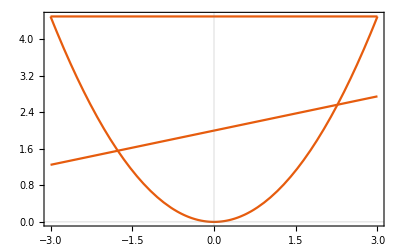

```mathematica
Show[Plot[f, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"], Plot[2+0.25*x, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"], Plot[ymax1, {x,xmin1,xmax1},PlotRange->{{xmin1,ymin1},{ymin1,ymax1}}, PlotTheme->"Scientific"]]
```

N[Integrate[Integrate[density in kg/m^3, {y because dy, (equation of boat is bottom limit, top limit aka height of boat)}], {x because dx, bottom x limit, top x limit}]]

```mathematica
N[Integrate[Integrate[100, {y, f, 4.5} ],{x, -3, 3}]]
```

1800.

N[(1/mass from last cell)*Integrate[Integrate[density*y,{y because dy, equation of hull is bottom limit, height of boat}], {x because dx, left x limit, right x limit }

```mathematica
N[(1/%)*Integrate[Integrate[100*y, {y, (x^2)/2, 4.5} ],{x, -3, 3}]]
```

2.7

Plot::plln: Limiting value xmin in {Charting`Private`pvar$267997,xmin,3} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[x^2/2,{x,xmin,3},PlotRange→{{-3,3},{0,4.5}},PlotTheme→Scientific],].

Plot::plln: Limiting value xmin in {Charting`Private`pvar$268028,xmin,3.} is not a machine-sized real number.

Plot::plln: Limiting value xmin in {Charting`Private`pvar$268053,xmin,3.} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Plot[x^2 0.5,{x,xmin,3.},PlotRange→{{-3.,3.},{0.,4.5}},PlotTheme→Scientific],].

Show::gcomb: Could not combine the graphics objects in Show[Plot[x^2/2,{x,xmin,3},PlotRange→{{-3,3},{0,4.5}},PlotTheme→Scientific],].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

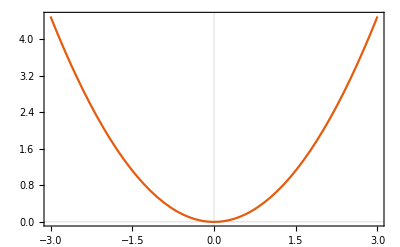

```mathematica
Show[Plot[((x^2)/2), {x,-3,3},PlotRange->{{-3,3},{0,4.5}}, PlotTheme->"Scientific"],Plot[%, {x,-3,3},PlotRange->{{-3,3},{0,4.5}}, PlotTheme->"Scientific"] ]
```